#### Exercise 3.1.1

```mathematica
f[x_, r_] = 1 + r x + x^2;
```

```mathematica
Solve[{f[x, r] ==0 && D[f[x, r],x] == 0}, {x, r}]
```

{{x→-1,r→2},{x→1,r→-2}}

```mathematica
Series[f[x, r], {x, -1, 2}, {r, 2, 1}] //Normal // Simplify
```

1+r x+x^2

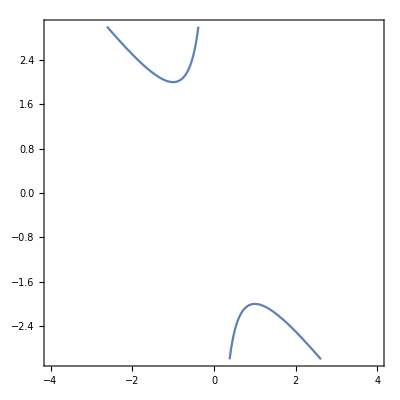

```mathematica
ContourPlot[f[x, r] == 0 , {x, -4, 4}, {r, -3, 3}]
```

#### Exercise 3.1.2

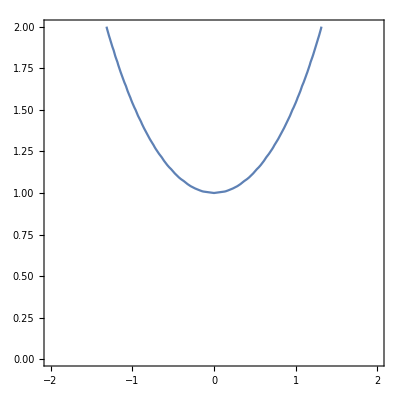

```mathematica
f[x_, r_] := r - Cosh[x]
ContourPlot[f[x, r]==0, {x, -2, 2}, {r, 0, 2}]
```

#### Exercise 3.1.3

```mathematica
Clear[f]
f[x_, r_] := r + x - Log[1+x];
```

```mathematica
Series[f[x, r], {x, x0, 2}] // Normal
```

r+x0+(x-x0)^2/(2 (1+x0)^2)+((x-x0) x0)/(1+x0)-Log[1+x0]

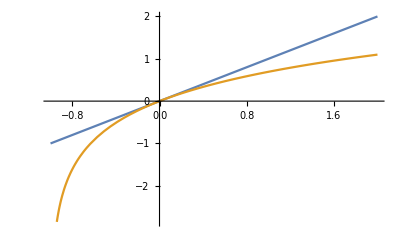

```mathematica
Plot[{x,Log[1+x]}, {x, -1, 2}]
```

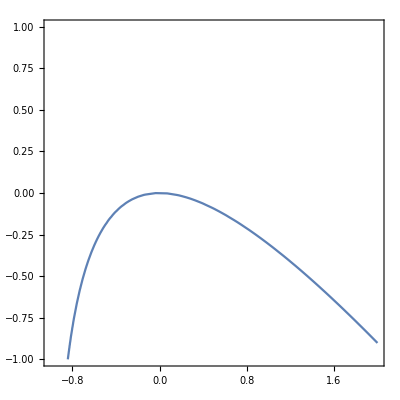

```mathematica
ContourPlot[r+x-Log[1+x]==0, {x, -1, 2}, {r, -1, 1}]
```

#### Exercise 3.1.4

```mathematica
Clear[f]
f[x_, r_]:= r + x/2-x/(1+x)
```

```mathematica
Solve[f[x, r]==0 && D[f[x, r], x]==0, {x,r}]
```

{{x→-1-√2,r→1/2 (3+2 √2)},{x→-1+√2,r→1/2 (3-2 √2)}}

```mathematica
Series[f[x, r], {x, -1+√2, 2}, {r,1/2 (3-2 √2),1}] // Normal
```

1/2 (-3+2 √2)+r+(1-√2+x)^2/(2 √2)

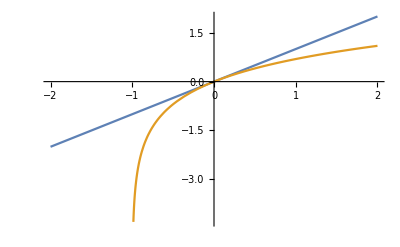

```mathematica
Plot[{x, Log[1+x]}, {x,-2,2}]
```

#### Exercise 3.2.2

```mathematica
Clear[f]
```

```mathematica
f[x_, r_] := r x - Log[1+x]
Manipulate[Plot[{r x, Log[1+x]}, {x,-1,4 }], {{r, 0}, -2, 2}]
```

```mathematica
Series[f[x, r], {x, 0, 2}] // Normal
```

(-1+r) x+x^2/2

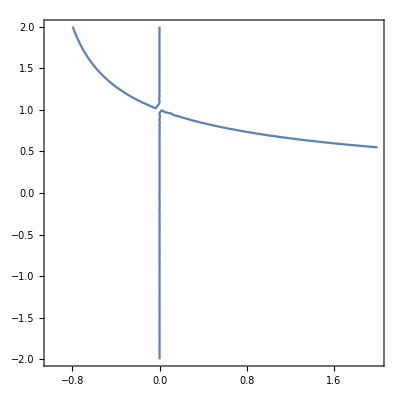

```mathematica
ContourPlot[f[x,r]==0, {x, -1, 2}, {r, -2, 2}]
```

```mathematica
fApprox[x_,r_] = Series[f[x, r], {x, 0, 2}] // Normal;
Solve[fApprox[x, r] ==0 && D[fApprox[x, r], x] == 0, {x,r}]
```

{{x→0,r→1}}

#### Exercise 3.2.3

```mathematica
Clear[f]
f[x_, r_] := x - r x(1-x)
Solve[f[x, r] ==0, x]
```

{{x→0},{x→(-1+r)/r}}

```mathematica
Solve[f[x, r] ==0 && D[f[x, r], x] == 0, {x, r}]
```

{{x→0,r→1},{x→0,r→1}}

```mathematica
Manipulate[Plot[ {x, r x (1-x)}, {x, -1, 1.5}, PlotRange->{-0.5, 0.5}], {{r,0}, -2, 2}]
```

```mathematica
Solve[f[x, r] ==0 && D[f[x, r], x] == 0, {x, r}]
```

{{x→0,r→1},{x→0,r→1}}

```mathematica
D[f[x, r], x] // Simplify
```

1+r (-1+2 x)

```mathematica
Series[f[x, r],{x, 0, 2} ]// Normal
```

(1-r) x+r x^2

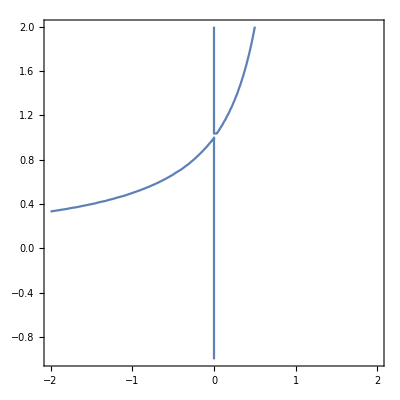

```mathematica
ContourPlot[f[x, r] ==0, {x, -2,2}, {r, -1, 2}]
```

#### Exercise 3.2.4

```mathematica
Clear[f]
f[x_, r_] := x(r - Exp[x])
```

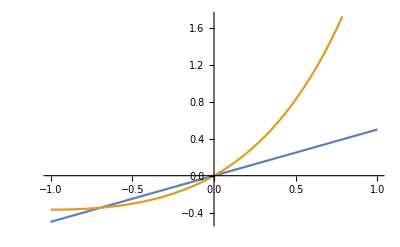

```mathematica
Plot[{0.5x, x Exp[x]}, {x, -1, 1}]
```

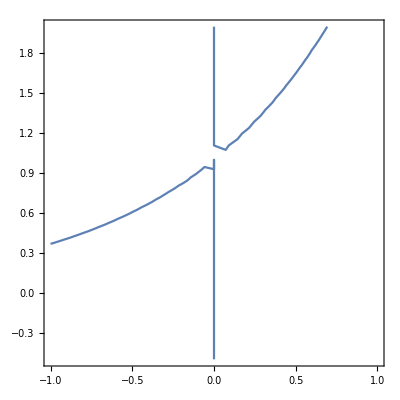

```mathematica
ContourPlot[f[x, r]==0, {x,-1, 1}, {r, -0.5, 2}]
```

```mathematica
Series[x Exp[x], {x, 0, 2}]//Normal
```

x+x^2

#### Exercise 3.4.1

```mathematica
Clear[f]
f[x, r] := rx + 4 x^3
```

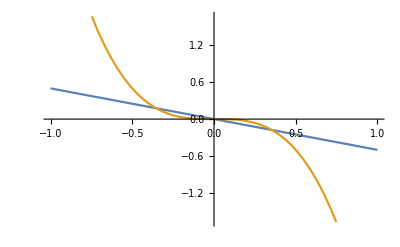

```mathematica
Plot[{-0.5x, -4 x^3}, {x, -1,1}]
```

#### Exercise 3.4.2

```mathematica
Clear[f]
f[x_, r_]:= r x - Sinh[x]
```

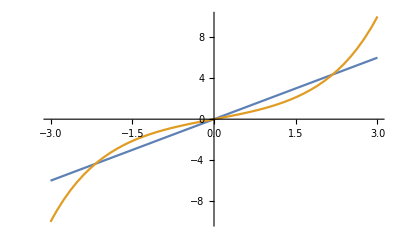

```mathematica
Plot[{2x, Sinh[x]}, {x, -3, 3}]
```

#### Exercise 3.4.3

```mathematica
Clear[f]
f[x_, r_]:= r x - 4 x^3
```

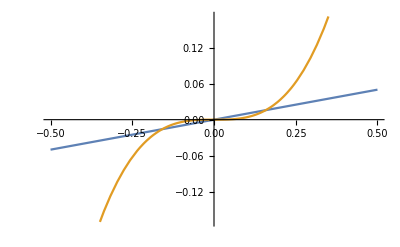

```mathematica
Plot[{0.1x, 4 x^3}, {x, -0.5, 0.5}]
```

#### Exercise 3.4.4

```mathematica
Clear[f]
f[x_, r_] := x + (r x)/(1 + x^2)
```

```mathematica
Manipulate[Plot[{r x^3, (r+1)x}, {x, -1, 1},PlotLegends-> {"h2", "h1"}, PlotRange->{-0.6, 0.6}], {{r, 0}, -2, 1}]
```

```mathematica
Solve[f[x, r] == 0 && D[f[x, r], x] == 0, {x, r}]
```

{{x→0,r→-1}}

```mathematica
Series[(r x)/(1 + x^2), {x, 0, 3}]
```

r x-r x^3+O[x]^4

```mathematica
f[0.5, -2]
```

-0.3

## Chapter 4

```mathematica
-Sin[(4π)/3]
```

(√3)/2

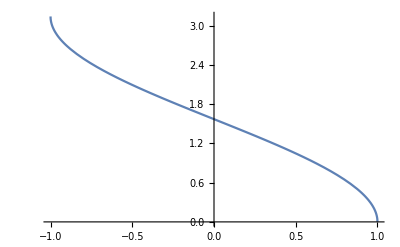

```mathematica
Plot[ArcCos[x], {x, -1, 1}]
```

```mathematica
π+π/3
```

(4 π)/3

```mathematica
π-π/3
```

```mathematica
ArcCos[1]
```

0

```mathematica
2π - ArcCos[1]
```

2 π

```mathematica
π/2+π
```

(3 π)/2

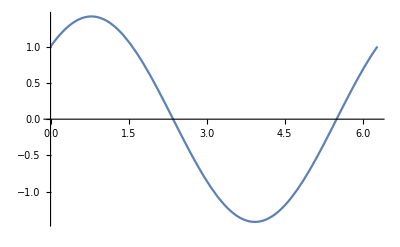

```mathematica
Plot[Sin[x] + Cos[x], {x, 0, 2π}]
```

```mathematica
(π+ π/2)/2
```

(3 π)/4

```mathematica
Sin[7 π/4]
```

-1/(√2)

```mathematica
-Cos[7 π/4]
```

-1/(√2)

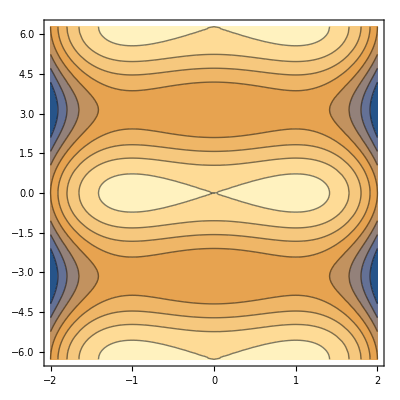

```mathematica
ContourPlot[Cos[y]- x^2/2(x^2/2-1), {x, -2, 2},{y, -2π, 2π}]
```

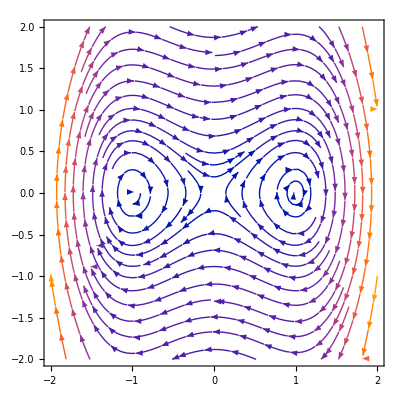

```mathematica
StreamPlot[{Sin[y], x-x^3}, {x, -2, 2},{y, -2,2}]
```

```mathematica
A = {{0, -Cos[y]}, {1-3 x^2, 0}};
MatrixForm[A]
```

(0 | -Cos[y]
1-3 x^2 | 0)

```mathematica
Av = A /. {x->0, y-> 0};
Av // MatrixForm
```

(0 | -1
1 | 0)

```mathematica
Eigenvalues[Av]
```

{ⅈ,-ⅈ}

```mathematica
Det[Av]
```

1

#### Exercise 6.3.4

```mathematica
Solve[x+y-x^3==0 && -y==0, {x, y}]
```

{{x→1,y→0},{x→0,y→0},{x→-1,y→0}}

```mathematica
A = {{1-3 x^2, 1}, {0, -1}};
MatrixForm[A]
```

(1-3 x^2 | 1
0 | -1)

```mathematica
Eigenvalues[A /. {x-> 1}]
Eigenvectors[A /. {x-> 1}]
```

{-2,-1}

{{1,0},{1,1}}

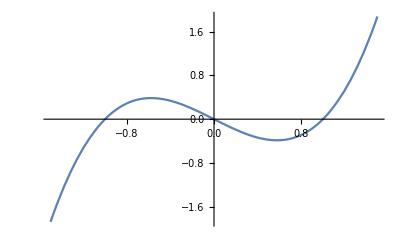

```mathematica
Plot[x^3-x, {x, -1.5, 1.5}]
```

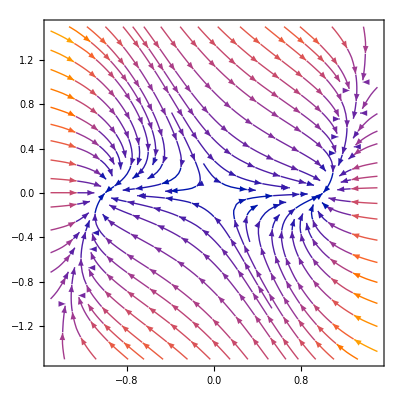

```mathematica
StreamPlot[{x +y-x^3,-y}, {x, -1.5, 1.5}, {y, -1.5, 1.5}]
```

#### 6.3.5

```mathematica
xp =(π+(3π)/2)/2
```

(5 π)/4

```mathematica
Cos[(5π)/4]
```

-1/(√2)

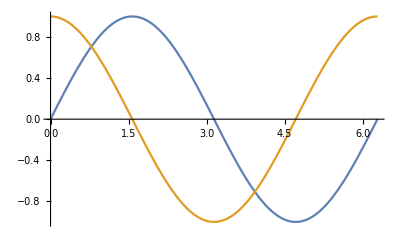

```mathematica
Plot[{Sin[x], Cos[x]}, {x, 0, 2π}]
```

```mathematica
A = {{0, Cos[y]}, {-Sin[x], 0}};
MatrixForm[A]
```

(0 | Cos[y]
-Sin[x] | 0)

If k mod 2 = 0; we have a center

```mathematica
res = A /.{x-> π/2, y-> 2π};
Tr[res]
Det[res]
```

0

1

If k mod 2 = 1; we have a saddle

```mathematica
res = A /.{x-> π/2, y-> π};
Tr[res]
Det[res]
```

0

-1

```mathematica
Eigenvectors[res]
```

{{1,1},{-1,1}}

```mathematica
Eigenvalues[res]
```

{-1,1}

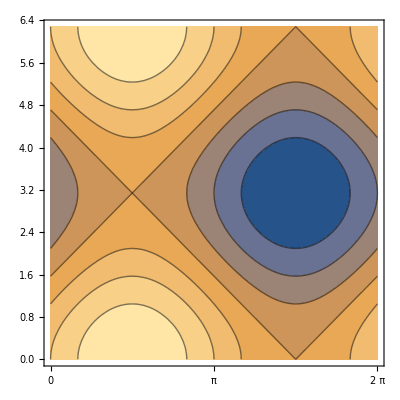

```mathematica
ContourPlot[Sin[x]+Cos[y], {x,0, 2π}, {y, 0, 2π}, FrameTicks->{Range[-2Pi,2Pi,Pi/4],Automatic}]
```

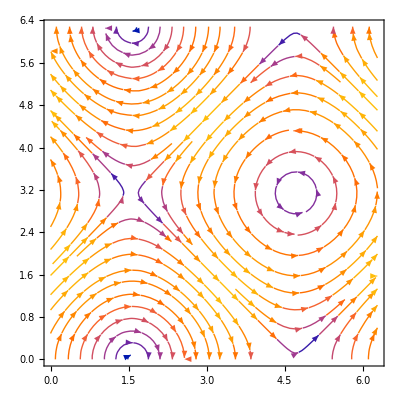

```mathematica
StreamPlot[{Sin[y], Cos[x]}, {x, 0, 2π}, {y, 0, 2π}]
```

#### 6.3.6

```mathematica
Solve[x y -1 == 0 && x - y^3==0, {x, y}]
```

{{x→-1,y→-1},{x→ⅈ,y→-ⅈ},{x→-ⅈ,y→ⅈ},{x→1,y→1}}

```mathematica
A = {{y, x}, {1, -3 y^2}};
A // MatrixForm
```

(y | x
1 | -3 y^2)

```mathematica
Av = A /. {x-> 1, y-> 1};
MatrixForm[Av]
```

(1 | 1
1 | -3)

```mathematica
Eigenvalues[Av]
```

{-1-√5,-1+√5}

```mathematica
Simplify[-2-√5+1/(√5)]
```

-2-4/(√5)

```mathematica
Eigenvectors[Av]
```

{{2-√5,1},{2+√5,1}}

```mathematica
-1-√5+3 // N
```

-0.236068

```mathematica
-1+√5+3
```

```mathematica
2+√5//N
```

4.23607

```mathematica
Eigenvectors[{{a, b}, {c, d}}] /. {a+d-> τ, a d -b c-> Δ}
```

{{-(-a+d+√(a^2+4 b c-2 a d+d^2))/(2 c),1},{-(-a+d-√(a^2+4 b c-2 a d+d^2))/(2 c),1}}

```mathematica
Av = A /. {x-> -1, y-> -1};
MatrixForm[Av]
```

(-1 | -1
1 | -3)

```mathematica
Eigenvalues[Av]
```

{-2,-2}

```mathematica
Eigenvectors[Av]
```

{{1,1},{0,0}}

```mathematica
JordanDecomposition[Av] [[1]] // MatrixForm
```

(1 | 1
1 | 0)

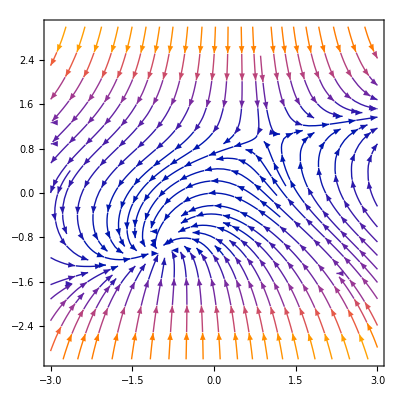

```mathematica
StreamPlot[{x y - 1, x-y^3}, {x, -3, 3}, {y, -3, 3}]
```

## Chapter 7

#### Exercise 7.3.1

```mathematica
f[x_, y_]:= x-y-x(x^2+5 y^2) (*x dot*)
g[x_, y_]:= x+y-y(x^2+y^2)   (*y dot*)
```

```mathematica
Jac = {Grad[f[x, y], {x, y}], Grad[g[x, y], {x, y}]};
Jac // MatrixForm
```

(1-3 x^2-5 y^2 | -1-10 x y
1-2 x y | 1-x^2-3 y^2)

```mathematica
Jac /. {x->0, y->0} // MatrixForm
```

(1 | -1
1 | 1)

Computing the system in terms of ṙ and θ̇

```mathematica
rdot =((x f[x, y] + y g[x, y])  /. {x-> r Cos[θ], y-> r Sin[θ]} // Simplify )/r
```

1/2 r (2-3 r^2+r^2 Cos[4 θ])

```mathematica
θdot =((x g[x, y] - y f[x, y]) /. { x-> r Cos[θ], y -> r Sin[θ]}) / r^2 //TrigReduce//  FullSimplify
```

1+4 r^2 Cos[θ] Sin[θ]^3

Next, we determine the circle of maximum radius centered at the origin, such that all trajectories have  radially outward component to it

```mathematica
Solve[1/2 r (2-3 r^2+r^2 Cos[4 θ]) == 0, r]
```

{{r→0},{r→-(√2)/(√(3-Cos[4 θ]))},{r→(√2)/(√(3-Cos[4 θ]))}}

```mathematica
θdot /. {r->(√2)/(√(3-Cos[4 θ]))}
```

#### Exercise 7.3.3

Show that the following system has a period solution

```mathematica
f[x_, y_] := x - y - x^3
g[x_, y_] := x + y - y^3
```

```mathematica
(x f[x, y] + y g[x, y]) / r /. {x -> r Cos[θ], y-> r Sin[θ]} // Simplify
```

```mathematica
-1/4 r (-4+3 r^2+r^2 S)
```

```mathematica
(x g[x, y] - y f[x, y]) / r^2 /. {x -> r Cos[θ], y-> r Sin[θ]} //  Simplify
```

1+1/4 r^2 Sin[4 θ]

```mathematica
Solve[1/4 (4 r-3 r^3-r^3 Cos[4 θ]) == 0, r]
```

{{r→0},{r→-2/(√(3+Cos[4 θ]))},{r→2/(√(3+Cos[4 θ]))}}

```mathematica
1+1/4 r^2 Sin[4 θ] /. {r->2/(√(3+Cos[4 θ]))}
```

1+Sin[4 θ]/(3+Cos[4 θ])

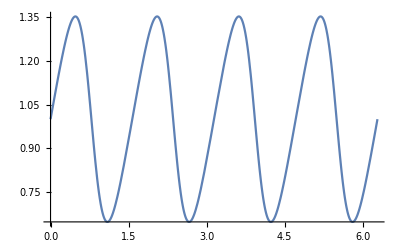

```mathematica
Plot[1+Sin[4 θ]/(3+Cos[4 θ]),{θ,0,2 π}]
```

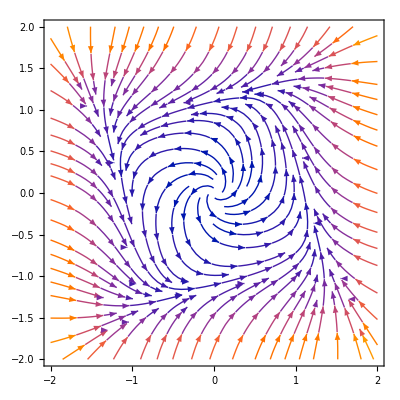

```mathematica
StreamPlot[{f[x, y], g[x, y]}, {x,-2, 2 }, {y, -2, 2}]
```

```mathematica
Sin[x]^4 + Cos[x]^4
```

Cos[x]^4+Sin[x]^4

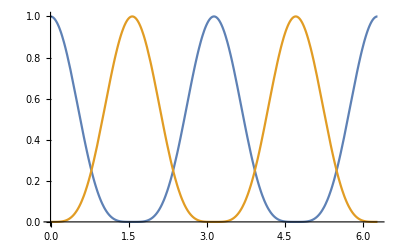

```mathematica
Plot[{Cos[x]^4,Sin[x]^4},{x,0, 2π}]
```

```mathematica
Solve[Sin[x]^4 ==Cos[x]^4, x]
```

{{x→ConditionalExpression[-(3 π)/4+2 π C[1], C[1]∈ℤ]},{x→ConditionalExpression[-π/4+2 π C[1], C[1]∈ℤ]},{x→ConditionalExpression[π/4+2 π C[1], C[1]∈ℤ]},{x→ConditionalExpression[(3 π)/4+2 π C[1], C[1]∈ℤ]}}

```mathematica
2 Cos[π/4]^4
```

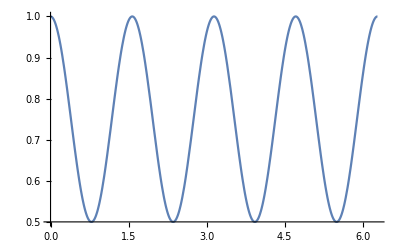

```mathematica
Plot[Cos[x]^4+Sin[x]^4,{x,0, 2π}]
```

#### Exercise 7.3.4

```mathematica
f[x_, y_] := x(1-4 x^2-y^2)-1/2 y(1+x)
g[x_, y_]:= y(1-4 x^2-y^2)+2x(1+x)
```

```mathematica
Jac ={Grad[f[x, y], {x, y}], Grad[g[x, y], {x, y}]};
Jac // MatrixForm
```

(1-12 x^2-y/2-y^2 | 1/2 (-1-x)-2 x y
2 x+2 (1+x)-8 x y | 1-4 x^2-3 y^2)

```mathematica
MatrixForm[Jac /. {x-> 0, y-> 0}]
```

(1 | -1/2
2 | 1)

```mathematica
Vdot =2(1-4 x^2-y^2)(-8x f[x,y]-2y g[x, y])
```

2 (1-4 x^2-y^2) (-8 x (-1/2 (1+x) y+x (1-4 x^2-y^2))-2 y (2 x (1+x)+y (1-4 x^2-y^2)))

```mathematica
FullSimplify[Vdot]
```

-4 (-1+4 x^2+y^2)^2 (4 x^2+y^2)

```mathematica
FullSimplify[Vdot] /. {x-> r Cos[θ]/2, y-> r Sin[θ]} // FullSimplify
```

-4 r^2 (-1+r^2)^2

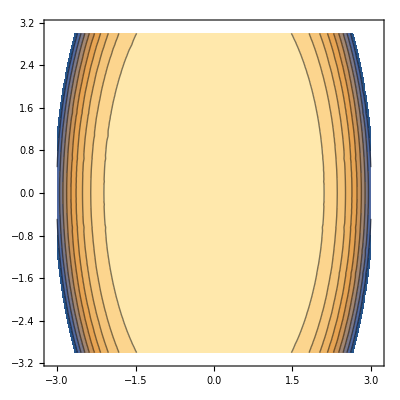

```mathematica
ContourPlot[FullSimplify[Vdot], {x, -3, 3}, {y, -3, 3}]
```

#### Exercise 7.3.5

```mathematica
Clear[f, g]
```

```mathematica
f[x_, y_]:= -x-y+x(x^2+2 y^2)
g[x_, y_]:= x-y+y(x^2+2 y^2)
```

```mathematica
x f[x,y]+y g[x, y] /. {x -> r Cos[θ], y-> r Sin[θ]} // Simplify
```

-1/2 r^2 (2-3 r^2+r^2 Cos[2 θ])

```mathematica
-r^2+r^4(1+Sin[θ]^2) - (-1/2 r^2 (2-3 r^2+r^2 Cos[2 θ])) // Simplify
```

0

```mathematica
x g[x, y]- y f[x, y] /. {x-> r Cos[θ], y-> r Sin[θ]}// Simplify
```

r^2

```mathematica
Solve[f[x, y]==0 && g[x, y]==0, {x, y}]
```

{{x→0,y→0},{x→-√(-1-ⅈ),y→-ⅈ √(-1-ⅈ)},{x→√(-1-ⅈ),y→ⅈ √(-1-ⅈ)},{x→-√(-1+ⅈ),y→ⅈ √(-1+ⅈ)},{x→√(-1+ⅈ),y→-ⅈ √(-1+ⅈ)}}

#### Exercise 7.3.7

```mathematica
Clear[f, g, a, b]
f[x_, y_] := y + a x(1-2b- r^2)
g[x_, y_]:= -x + a y (1- r^2)
```

```mathematica
(x f[x, y] + y g[x, y]) / r  /. {x-> r Cos[θ], y-> r Sin[θ]} // Simplify
```

-a r (-1+b+r^2+b Cos[2 θ])

```mathematica
(x g[x, y] - y f[x, y]) / r^2 /. {x-> r Cos[θ], y-> r Sin[θ]}  // FullSimplify
```

-1+a b Sin[2 θ]

The plot in Cartesian coordinates

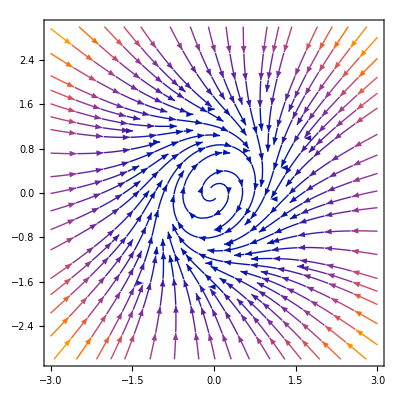

```mathematica
a = 0.6; b  =0.4;
StreamPlot[{f[x, y] /. {r^2-> x^2+y^2}, g[x, y]/. {r^2-> x^2+y^2}}, {x, -3, 3}, {y, -3, 3}]
```

The plot in polar coordinates

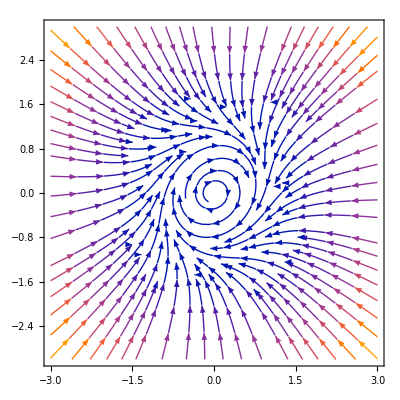

```mathematica
field={a r(1-r^2-2b Cos[θ]^2),-1 + a b Sin[2θ]};
StreamPlot[Evaluate@TransformedField["Polar"->"Cartesian",field,{r,θ}->{x,y}],{x,-3,3},{y,-3, 3}]
```

#### Exercise 7.3.8

If we look for a trapping region, we notice that it exists for μ <=  1 and it does not exist for μ > 1

```mathematica
field = {r(1 - r^2) + μ r Cos[θ], 1}; 
Manipulate[
StreamPlot[Evaluate[TransformedField["Polar" -> "Cartesian", 
     field /. {μ -> μv}, {r, θ} -> {x, y}]], {x, -1.5, 1.5}, {y, -1.5, 1.5}],
{μv, 0.1, 5}]
```